```mathematica
ColorSSSMatrix[graph_,graphFormat_:FormatGraph,vertices_:Null, sols_]:=Block[{result,bg, sorted,sums},
sorted=Graph[Sort[VertexList[graph]],Sort[EdgeList[graph],EdgeComp]];
sums=Association[];
Table[sums[v]={0,0},{v,VertexList[sorted]}];
result=TableForm[
Table[
bg=None;
Framed[
With[
{
mat=ColorSubMatrix[sols,i,j]
},
sums[i]=sums[i]+mat;
sums[j]=sums[j]+mat;
If[mat[[1]]==0,bg=LightRed];
If[MemberQ[vertices,i]&&MemberQ[vertices,j],bg=LightRed];
If[i==j,bg=LightYellow];
If[EdgeQ[sorted,i<->j],bg=LightBlue];
TableForm[mat]
],
Background->bg
],
{i,VertexList[sorted]},
{j,VertexList[sorted]}],
TableHeadings->{Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,VertexList[sorted]], Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,VertexList[sorted]]},
TableSpacing->{0, 0}
];
{graphFormat[sorted],result,
TableForm[
Map[Framed[{N[#[[1]]/#[[2]]],#[[1]]/#[[2]],TableForm[#]}]&,Values[sums]],
TableHeadings->{Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,Keys[sums]], Map[If[MemberQ[vertices,#],Style[#,Bold,Red],#]&,Keys[sums]]},
TableSpacing->{0, 0}
],
Total[Map[sums[#][[1]]&,Keys[sums]]]/Total[Map[sums[#][[2]]&,Keys[sums]]],
N[Total[Map[sums[#][[1]]&,Keys[sums]]]/Total[Map[sums[#][[2]]&,Keys[sums]]]]
}
]
```

```mathematica
CalcEqual[sols_,v1_,v2_]:=Block[
{couplesols=Map[{Symbol["x"<>ToString[v1]],Symbol["x"<>ToString[v2]]}/.#&,sols]},
Length[Select[couplesols,#[[1]]==#[[2]]&]]
]
```

```mathematica
AlfaBetaQuadrupel[g_,v1_,v2_,v3_,v4_]:=Block[
{ 
lambda,
empty,sols,
hor,solsh,
vert,solsv,
alfa,beta,alfa1
},

PrintTemporary["Solving g.." ];
empty=g;
sols=Solve[ToEquations[empty],SymbolRange[empty]];
lambda=ChromaticPolynomial[empty,4];
alfa=CalcEqual[sols,v1,v3];
beta=CalcEqual[sols,v2,v4];

hor = VertexContract[g,{v2,v4}];
PrintTemporary["Solving hor.." ];
solsh=Solve[ToEquations[hor],SymbolRange[hor]];
alfa1=CalcEqual[solsh,v1,v3];

{{lambda, alfa,beta,alfa1}/24,g}
]
```

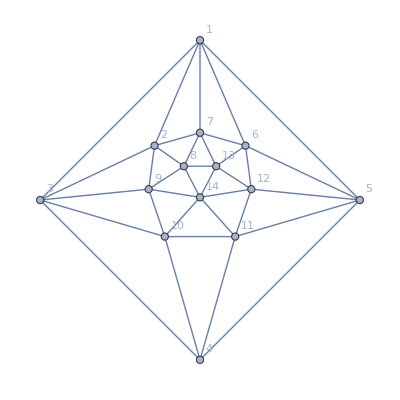
{{34,14,18,6},-Graphics-}

```mathematica
AlfaBetaQuadrupel[Graph[EdgeDelete[Graph[plantri[[2]]],1<->4],GraphLayout->"TutteEmbedding", VertexLabels->"Name"],1,3,4,5]
```

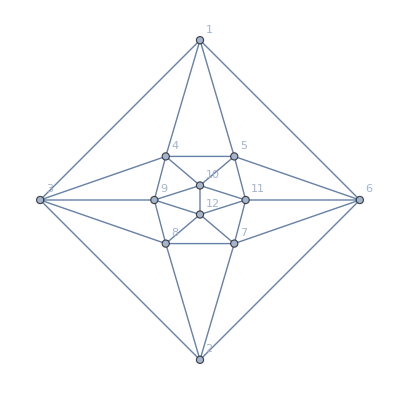
{{18,8,6,2},-Graphics-}

```mathematica
AlfaBetaQuadrupel[Graph[EdgeDelete[Graph[plantri[[1]]],1<->2],GraphLayout->"TutteEmbedding", VertexLabels->"Name"],1,6,2,3]
```

```mathematica
AlfaBetaQuadrupel[ggg,1,6,5,4]
```

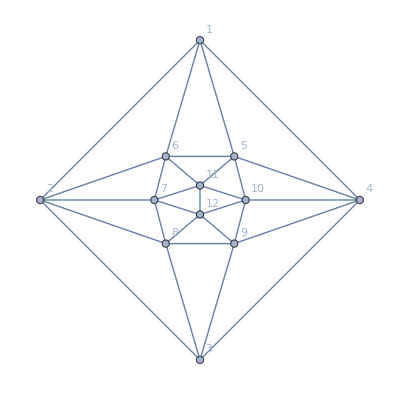
{{18,8,6,2},-Graphics-}

```mathematica
AlfaBetaQuadrupel[Graph[EdgeDelete[Graph[plantri[[1]]],1<->3],GraphLayout->"TutteEmbedding", VertexLabels->"Name"],1,4,3,2]
```

```mathematica
Graph[EdgeDelete[Graph[plantri[[1]]],1<->3],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

-Graphics-

```mathematica
ggg=Graph[EdgeDelete[Graph[plantri[[1]]],1<->2],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

-Graphics-

```mathematica
ggg=Graph[EdgeDelete[Graph[plantri[[2]]],1<->4],GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

-Graphics-

```mathematica
FindFace[g_,e_]:=Block[{h,n1,n2,i},
h=EdgeDelete[g,e];
n1=NeighborhoodGraph[h,e[[1]]];
n2=NeighborhoodGraph[h,e[[2]]];
i=Intersection[VertexList[n1],VertexList[n2]];
{e[[1]],i[[1]],e[[2]],i[[2]]}
]
```

```mathematica
EdgeList[Graph[plantri[[1]]]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->6,2<->7,2<->8,2<->3,3<->8,3<->9,3<->4,4<->9,4<->10,4<->5,5<->10,5<->11,5<->6,6<->11,6<->7,7<->11,7<->12,7<->8,8<->12,8<->9,9<->12,9<->10,10<->12,10<->11,11<->12}

```mathematica
FindFace[Graph[plantri[[1]]],1<->2]
```

{1,3,2,6}

```mathematica
CalcQuadri[g_,v_]:=Block[{h,b,b2,lambda,alfa,beta,alfa1, hasEdge},
alfa=ChromaticPolynomial[EdgeContract[g,v[[1]]<->v[[3]]],4]/24;
h=EdgeDelete[g,v[[1]]<->v[[3]]];
lambda=ChromaticPolynomial[h,4]/24;
b=VertexContract[h,{v[[2]],v[[4]]}];
beta=ChromaticPolynomial[b,4]/24;
b2=VertexContract[h,{v[[2]],v[[4]]}];
b2=VertexContract[b2,{v[[1]],v[[3]]}];
alfa1=ChromaticPolynomial[b2,4]/24;
{λ->lambda,α+β->alfa+beta,α->alfa,β->beta,α1->alfa1}
]
```

```mathematica
{18,8,6,2}
```

```mathematica
CalcQuadri[g_,v_]:=Block[{h,b,b2,lambda,alfa,beta,alfa1, hasEdge},
hasEdge=EdgeQ[g,v[[2]]<->v[[4]]];
alfa=ChromaticPolynomial[EdgeContract[g,v[[1]]<->v[[3]]],4]/24;
h=EdgeDelete[g,v[[1]]<->v[[3]]];
lambda=ChromaticPolynomial[h,4]/24;
b=VertexContract[h,{v[[2]],v[[4]]}];
beta=ChromaticPolynomial[b,4]/24;
b2=VertexContract[h,{v[[2]],v[[4]]}];
b2=VertexContract[b2,{v[[1]],v[[3]]}];
alfa1=ChromaticPolynomial[b2,4]/24;
{lambda,alfa+beta,alfa,beta,alfa1,Floor[((2*(alfa+beta)-lambda)+4)/5]-alfa1, hasEdge,Table[VertexDegree[g,v1],{v1,v}]}
]
```

```mathematica
Monitor[
Table[
With[
{g=Graph[plantri[[i]]]},
Table[
With[
{f=FindFace[g,e]},
{i,e,CalcQuadri[g,f]}
]
,{e,EdgeList[g]}]
],
{i,1,18}
],{i,e}]
```

{{{1,1<->2,{18,14,8,6,2,0}},{1,1<->3,{18,14,8,6,2,0}},{1,1<->4,{18,14,8,6,2,0}},{1,1<->5,{18,14,8,6,2,0}},{1,1<->6,{18,14,8,6,2,0}},{1,2<->6,{18,14,8,6,2,0}},{1,2<->7,{18,14,8,6,2,0}},{1,2<->8,{18,14,8,6,2,0}},{1,2<->3,{18,14,8,6,2,0}},{1,3<->8,{18,14,8,6,2,0}},{1,3<->9,{18,14,8,6,2,0}},{1,3<->4,{18,14,8,6,2,0}},{1,4<->9,{18,14,8,6,2,0}},{1,4<->10,{18,14,8,6,2,0}},{1,4<->5,{18,14,8,6,2,0}},{1,5<->10,{18,14,8,6,2,0}},{1,5<->11,{18,14,8,6,2,0}},{1,5<->6,{18,14,8,6,2,0}},{1,6<->11,{18,14,8,6,2,0}},{1,6<->7,{18,14,8,6,2,0}},{1,7<->11,{18,14,8,6,2,0}},{1,7<->12,{18,14,8,6,2,0}},{1,7<->8,{18,14,8,6,2,0}},{1,8<->12,{18,14,8,6,2,0}},{1,8<->9,{18,14,8,6,2,0}},{1,9<->12,{18,14,8,6,2,0}},{1,9<->10,{18,14,8,6,2,0}},{1,10<->12,{18,14,8,6,2,0}},{1,10<->11,{18,14,8,6,2,0}},{1,11<->12,{18,14,8,6,2,0}}},{{2,1<->2,{34,32,14,18,6,0}},{2,1<->3,{34,32,14,18,6,0}},{2,1<->4,{34,32,14,18,6,0}},{2,1<->5,{34,32,14,18,6,0}},{2,1<->6,{34,32,14,18,6,0}},{2,1<->7,{34,32,14,18,6,0}},{2,2<->7,{34,27,14,13,4,0}},{2,2<->8,{39,27,19,8,3,0}},{2,2<->9,{39,27,19,8,3,0}},{2,2<->3,{34,27,14,13,4,0}},{2,3<->9,{39,27,19,8,3,0}},{2,3<->10,{39,27,19,8,3,0}},{2,3<->4,{34,27,14,13,4,0}},{2,4<->10,{39,27,19,8,3,0}},{2,4<->11,{39,27,19,8,3,0}},{2,4<->5,{34,27,14,13,4,0}},{2,5<->11,{39,27,19,8,3,0}},{2,5<->12,{39,27,19,8,3,0}},{2,5<->6,{34,27,14,13,4,0}},{2,6<->12,{39,27,19,8,3,0}},{2,6<->13,{39,27,19,8,3,0}},{2,6<->7,{34,27,14,13,4,0}},{2,7<->13,{39,27,19,8,3,0}},{2,7<->8,{39,27,19,8,3,0}},{2,8<->13,{34,27,14,13,4,0}},{2,8<->14,{34,32,14,18,6,0}},{2,8<->9,{34,27,14,13,4,0}},{2,9<->14,{34,32,14,18,6,0}},{2,9<->10,{34,27,14,13,4,0}},{2,10<->14,{34,32,14,18,6,0}},{2,10<->11,{34,27,14,13,4,0}},{2,11<->14,{34,32,14,18,6,0}},{2,11<->12,{34,27,14,13,4,0}},{2,12<->14,{34,32,14,18,6,0}},{2,12<->13,{34,27,14,13,4,0}},{2,13<->14,{34,32,14,18,6,0}}},{{3,1<->2,{46,28,14,14,2,0}},{3,1<->3,{44,32,12,20,4,0}},{3,1<->4,{46,28,14,14,2,0}},{3,1<->5,{46,28,14,14,2,0}},{3,1<->6,{44,32,12,20,4,0}},{3,1<->7,{46,28,14,14,2,0}},{3,2<->7,{52,36,20,16,4,0}},{3,2<->8,{46,28,14,14,2,0}},{3,2<->9,{48,34,16,18,4,0}},{3,2<->3,{48,34,16,18,4,0}},{3,3<->9,{50,30,18,12,2,0}},{3,3<->10,{50,30,18,12,2,0}},{3,3<->4,{48,34,16,18,4,0}},{3,4<->10,{48,34,16,18,4,0}},{3,4<->11,{46,28,14,14,2,0}},{3,4<->5,{52,36,20,16,4,0}},{3,5<->11,{46,28,14,14,2,0}},{3,5<->12,{48,34,16,18,4,0}},{3,5<->6,{48,34,16,18,4,0}},{3,6<->12,{50,30,18,12,2,0}},{3,6<->13,{50,30,18,12,2,0}},{3,6<->7,{48,34,16,18,4,0}},{3,7<->13,{48,34,16,18,4,0}},{3,7<->8,{46,28,14,14,2,0}},{3,8<->13,{44,32,12,20,4,0}},{3,8<->14,{46,28,14,14,2,0}},{3,8<->15,{46,28,14,14,2,0}},{3,8<->9,{44,32,12,20,4,0}},{3,9<->15,{48,34,16,18,4,0}},{3,9<->10,{50,30,18,12,2,0}},{3,10<->15,{48,34,16,18,4,0}},{3,10<->11,{44,32,12,20,4,0}},{3,11<->15,{46,28,14,14,2,0}},{3,11<->14,{46,28,14,14,2,0}},{3,11<->12,{44,32,12,20,4,0}},{3,12<->14,{48,34,16,18,4,0}},{3,12<->13,{50,30,18,12,2,0}},{3,13<->14,{48,34,16,18,4,0}},{3,14<->15,{52,36,20,16,4,0}}},{{4,1<->2,{62,66,32,34,14,0}},{4,1<->3,{42,26,12,14,2,0}},{4,1<->4,{62,46,32,14,6,0}},{4,1<->5,{62,46,32,14,6,0}},{4,1<->6,{42,26,12,14,2,0}},{4,2<->6,{42,26,12,14,2,0}},{4,2<->7,{62,46,32,14,6,0}},{4,2<->8,{62,46,32,14,6,0}},{4,2<->3,{42,26,12,14,2,0}},{4,3<->8,{42,26,12,14,2,0}},{4,3<->9,{42,26,12,14,2,0}},{4,3<->10,{42,26,12,14,2,0}},{4,3<->4,{42,26,12,14,2,0}},{4,4<->10,{62,66,32,34,14,0}},{4,4<->11,{42,26,12,14,2,0}},{4,4<->5,{62,46,32,14,6,0}},{4,5<->11,{42,26,12,14,2,0}},{4,5<->12,{62,66,32,34,14,0}},{4,5<->6,{42,26,12,14,2,0}},{4,6<->12,{42,26,12,14,2,0}},{4,6<->13,{42,26,12,14,2,0}},{4,6<->7,{42,26,12,14,2,0}},{4,7<->13,{62,66,32,34,14,0}},{4,7<->14,{42,26,12,14,2,0}},{4,7<->8,{62,46,32,14,6,0}},{4,8<->14,{42,26,12,14,2,0}},{4,8<->9,{62,66,32,34,14,0}},{4,9<->14,{42,26,12,14,2,0}},{4,9<->15,{62,46,32,14,6,0}},{4,9<->10,{62,46,32,14,6,0}},{4,10<->15,{62,46,32,14,6,0}},{4,10<->11,{42,26,12,14,2,0}},{4,11<->15,{42,26,12,14,2,0}},{4,11<->16,{42,26,12,14,2,0}},{4,11<->12,{42,26,12,14,2,0}},{4,12<->16,{62,46,32,14,6,0}},{4,12<->13,{62,46,32,14,6,0}},{4,13<->16,{62,46,32,14,6,0}},{4,13<->14,{42,26,12,14,2,0}},{4,14<->16,{42,26,12,14,2,0}},{4,14<->15,{42,26,12,14,2,0}},{4,15<->16,{62,66,32,34,14,0}}},{{5,1<->2,{59,57,32,25,11,0}},{5,1<->3,{46,33,19,14,4,0}},{5,1<->4,{51,38,24,14,5,0}},{5,1<->5,{59,52,32,20,9,0}},{5,1<->6,{40,25,13,12,2,0}},{5,2<->6,{46,33,19,14,4,0}},{5,2<->7,{51,38,24,14,5,0}},{5,2<->8,{59,52,32,20,9,0}},{5,2<->3,{40,25,13,12,2,0}},{5,3<->8,{50,40,23,17,6,0}},{5,3<->9,{45,35,18,17,5,0}},{5,3<->10,{36,18,9,9,0,0}},{5,3<->4,{54,47,27,20,8,0}},{5,4<->10,{45,35,18,17,5,0}},{5,4<->11,{54,47,27,20,8,0}},{5,4<->5,{51,38,24,14,5,0}},{5,5<->11,{56,48,29,19,8,0}},{5,5<->12,{54,47,27,20,8,0}},{5,5<->6,{50,40,23,17,6,0}},{5,6<->12,{45,35,18,17,5,0}},{5,6<->13,{36,18,9,9,0,0}},{5,6<->7,{54,47,27,20,8,0}},{5,7<->13,{45,35,18,17,5,0}},{5,7<->14,{54,47,27,20,8,0}},{5,7<->8,{51,38,24,14,5,0}},{5,8<->14,{56,48,29,19,8,0}},{5,8<->9,{54,47,27,20,8,0}},{5,9<->14,{51,38,24,14,5,0}},{5,9<->15,{51,38,24,14,5,0}},{5,9<->10,{54,47,27,20,8,0}},{5,10<->15,{46,33,19,14,4,0}},{5,10<->16,{40,25,13,12,2,0}},{5,10<->11,{50,40,23,17,6,0}},{5,11<->16,{59,52,32,20,9,0}},{5,11<->12,{51,38,24,14,5,0}},{5,12<->16,{51,38,24,14,5,0}},{5,12<->13,{54,47,27,20,8,0}},{5,13<->16,{46,33,19,14,4,0}},{5,13<->15,{40,25,13,12,2,0}},{5,13<->14,{50,40,23,17,6,0}},{5,14<->15,{59,52,32,20,9,0}},{5,15<->16,{59,57,32,25,11,0}}},{{6,1<->2,{60,40,18,22,4,0}},{6,1<->3,{69,52,27,25,7,0}},{6,1<->4,{66,43,24,19,4,0}},{6,1<->5,{66,43,24,19,4,0}},{6,1<->6,{69,52,27,25,7,0}},{6,2<->6,{60,40,18,22,4,0}},{6,2<->7,{60,40,18,22,4,0}},{6,2<->8,{60,40,18,22,4,0}},{6,2<->9,{60,40,18,22,4,0}},{6,2<->10,{60,40,18,22,4,0}},{6,2<->3,{60,40,18,22,4,0}},{6,3<->10,{69,52,27,25,7,0}},{6,3<->11,{66,43,24,19,4,0}},{6,3<->4,{66,43,24,19,4,0}},{6,4<->11,{69,52,27,25,7,0}},{6,4<->12,{60,40,18,22,4,0}},{6,4<->5,{69,52,27,25,7,0}},{6,5<->12,{60,40,18,22,4,0}},{6,5<->13,{69,52,27,25,7,0}},{6,5<->6,{66,43,24,19,4,0}},{6,6<->13,{66,43,24,19,4,0}},{6,6<->7,{69,52,27,25,7,0}},{6,7<->13,{66,43,24,19,4,0}},{6,7<->14,{66,43,24,19,4,0}},{6,7<->8,{69,52,27,25,7,0}},{6,8<->14,{66,43,24,19,4,0}},{6,8<->15,{66,43,24,19,4,0}},{6,8<->9,{69,52,27,25,7,0}},{6,9<->15,{66,43,24,19,4,0}},{6,9<->16,{66,43,24,19,4,0}},{6,9<->10,{69,52,27,25,7,0}},{6,10<->16,{66,43,24,19,4,0}},{6,10<->11,{66,43,24,19,4,0}},{6,11<->16,{69,52,27,25,7,0}},{6,11<->12,{60,40,18,22,4,0}},{6,12<->16,{60,40,18,22,4,0}},{6,12<->15,{60,40,18,22,4,0}},{6,12<->14,{60,40,18,22,4,0}},{6,12<->13,{60,40,18,22,4,0}},{6,13<->14,{69,52,27,25,7,0}},{6,14<->15,{69,52,27,25,7,0}},{6,15<->16,{69,52,27,25,7,0}}},{{7,1<->2,{48,44,32,12,8,0}},{7,1<->3,{44,42,28,14,8,0}},{7,1<->4,{44,47,28,19,10,0}},{7,1<->5,{43,44,27,17,9,0}},{7,1<->6,{46,43,30,13,8,0}},{7,2<->6,{46,43,30,13,8,0}},{7,2<->7,{43,44,27,17,9,0}},{7,2<->8,{44,47,28,19,10,0}},{7,2<->3,{44,42,28,14,8,0}},{7,3<->8,{38,34,22,12,6,0}},{7,3<->9,{46,48,30,18,10,0}},{7,3<->4,{38,34,22,12,6,0}},{7,4<->9,{38,34,22,12,6,0}},{7,4<->10,{50,50,34,16,10,0}},{7,4<->11,{37,36,21,15,7,0}},{7,4<->5,{44,37,28,9,6,0}},{7,5<->11,{44,37,28,9,6,0}},{7,5<->12,{43,44,27,17,9,0}},{7,5<->6,{36,38,20,18,8,0}},{7,6<->12,{46,43,30,13,8,0}},{7,6<->13,{46,43,30,13,8,0}},{7,6<->7,{36,38,20,18,8,0}},{7,7<->13,{43,44,27,17,9,0}},{7,7<->14,{44,37,28,9,6,0}},{7,7<->8,{44,37,28,9,6,0}},{7,8<->14,{37,36,21,15,7,0}},{7,8<->15,{50,50,34,16,10,0}},{7,8<->9,{38,34,22,12,6,0}},{7,9<->15,{44,42,28,14,8,0}},{7,9<->10,{44,42,28,14,8,0}},{7,10<->15,{52,56,36,20,12,0}},{7,10<->16,{44,42,28,14,8,0}},{7,10<->11,{50,50,34,16,10,0}},{7,11<->16,{38,34,22,12,6,0}},{7,11<->17,{38,34,22,12,6,0}},{7,11<->12,{44,47,28,19,10,0}},{7,12<->17,{44,42,28,14,8,0}},{7,12<->13,{48,44,32,12,8,0}},{7,13<->17,{44,42,28,14,8,0}},{7,13<->14,{44,47,28,19,10,0}},{7,14<->17,{38,34,22,12,6,0}},{7,14<->16,{38,34,22,12,6,0}},{7,14<->15,{50,50,34,16,10,0}},{7,15<->16,{44,42,28,14,8,0}},{7,16<->17,{46,48,30,18,10,0}}},{{8,1<->2,{55,45,33,12,7,0}},{8,1<->3,{56,53,34,19,10,0}},{8,1<->4,{50,50,28,22,10,0}},{8,1<->5,{52,51,30,21,10,0}},{8,1<->6,{57,51,35,16,9,0}},{8,2<->6,{50,45,28,17,8,0}},{8,2<->7,{48,49,26,23,10,0}},{8,2<->8,{49,47,27,20,9,0}},{8,2<->3,{53,44,31,13,7,0}},{8,3<->8,{45,50,23,27,11,0}},{8,3<->9,{53,44,31,13,7,0}},{8,3<->10,{56,53,34,19,10,0}},{8,3<->4,{37,36,15,21,7,0}},{8,4<->10,{50,50,28,22,10,0}},{8,4<->11,{50,50,28,22,10,0}},{8,4<->12,{37,36,15,21,7,0}},{8,4<->5,{50,50,28,22,10,0}},{8,5<->12,{56,53,34,19,10,0}},{8,5<->13,{55,45,33,12,7,0}},{8,5<->6,{57,51,35,16,9,0}},{8,6<->13,{50,45,28,17,8,0}},{8,6<->7,{56,58,34,24,12,0}},{8,7<->13,{48,49,26,23,10,0}},{8,7<->14,{56,43,34,9,6,0}},{8,7<->15,{78,94,56,38,22,0}},{8,7<->8,{56,43,34,9,6,0}},{8,8<->15,{56,43,34,9,6,0}},{8,8<->9,{49,47,27,20,9,0}},{8,9<->15,{48,49,26,23,10,0}},{8,9<->16,{50,45,28,17,8,0}},{8,9<->10,{55,45,33,12,7,0}},{8,10<->16,{57,51,35,16,9,0}},{8,10<->11,{52,51,30,21,10,0}},{8,11<->16,{57,51,35,16,9,0}},{8,11<->17,{55,45,33,12,7,0}},{8,11<->12,{56,53,34,19,10,0}},{8,12<->17,{53,44,31,13,7,0}},{8,12<->14,{45,50,23,27,11,0}},{8,12<->13,{53,44,31,13,7,0}},{8,13<->14,{49,47,27,20,9,0}},{8,14<->17,{49,47,27,20,9,0}},{8,14<->15,{56,43,34,9,6,0}},{8,15<->17,{48,49,26,23,10,0}},{8,15<->16,{56,58,34,24,12,0}},{8,16<->17,{50,45,28,17,8,0}}},{{9,1<->2,{58,44,26,18,6,0}},{9,1<->3,{81,78,49,29,15,0}},{9,1<->4,{58,49,26,23,8,0}},{9,1<->5,{66,53,34,19,8,0}},{9,1<->6,{68,64,36,28,12,0}},{9,1<->7,{56,48,24,24,8,0}},{9,2<->7,{74,72,42,30,14,0}},{9,2<->8,{58,44,26,18,6,0}},{9,2<->9,{70,60,38,22,10,0}},{9,2<->3,{70,60,38,22,10,0}},{9,3<->9,{67,56,35,21,9,0}},{9,3<->10,{82,81,50,31,16,0}},{9,3<->4,{60,45,28,17,6,0}},{9,4<->10,{65,50,33,17,7,0}},{9,4<->11,{58,44,26,18,6,0}},{9,4<->5,{59,52,27,25,9,0}},{9,5<->11,{60,55,28,27,10,0}},{9,5<->12,{64,52,32,20,8,0}},{9,5<->6,{66,48,34,14,6,0}},{9,6<->12,{72,56,40,16,8,0}},{9,6<->13,{66,58,34,24,10,0}},{9,6<->7,{58,54,26,28,10,0}},{9,7<->13,{62,56,30,26,10,0}},{9,7<->14,{58,54,26,28,10,0}},{9,7<->8,{56,48,24,24,8,0}},{9,8<->14,{68,64,36,28,12,0}},{9,8<->15,{66,53,34,19,8,0}},{9,8<->16,{58,49,26,23,8,0}},{9,8<->9,{81,78,49,29,15,0}},{9,9<->16,{60,45,28,17,6,0}},{9,9<->10,{82,81,50,31,16,0}},{9,10<->16,{65,50,33,17,7,0}},{9,10<->11,{96,98,64,34,20,0}},{9,11<->16,{58,44,26,18,6,0}},{9,11<->15,{60,55,28,27,10,0}},{9,11<->17,{64,62,32,30,12,0}},{9,11<->12,{64,62,32,30,12,0}},{9,12<->17,{62,56,30,26,10,0}},{9,12<->13,{68,54,36,18,8,0}},{9,13<->17,{68,54,36,18,8,0}},{9,13<->14,{66,58,34,24,10,0}},{9,14<->17,{72,56,40,16,8,0}},{9,14<->15,{66,48,34,14,6,0}},{9,15<->17,{64,52,32,20,8,0}},{9,15<->16,{59,52,27,25,9,0}}},{{10,1<->2,{74,62,34,28,10,0}},{10,1<->3,{64,42,24,18,4,0}},{10,1<->4,{84,72,44,28,12,0}},{10,1<->5,{64,42,24,18,4,0}},{10,1<->6,{74,62,34,28,10,0}},{10,2<->6,{78,94,38,56,22,0}},{10,2<->7,{74,62,34,28,10,0}},{10,2<->8,{74,62,34,28,10,0}},{10,2<->9,{78,94,38,56,22,0}},{10,2<->3,{74,62,34,28,10,0}},{10,3<->9,{74,62,34,28,10,0}},{10,3<->10,{64,42,24,18,4,0}},{10,3<->4,{84,72,44,28,12,0}},{10,4<->10,{84,72,44,28,12,0}},{10,4<->11,{84,72,44,28,12,0}},{10,4<->5,{84,72,44,28,12,0}},{10,5<->11,{64,42,24,18,4,0}},{10,5<->12,{74,62,34,28,10,0}},{10,5<->6,{74,62,34,28,10,0}},{10,6<->12,{78,94,38,56,22,0}},{10,6<->13,{74,62,34,28,10,0}},{10,6<->7,{74,62,34,28,10,0}},{10,7<->13,{64,42,24,18,4,0}},{10,7<->14,{84,72,44,28,12,0}},{10,7<->8,{64,42,24,18,4,0}},{10,8<->14,{84,72,44,28,12,0}},{10,8<->15,{64,42,24,18,4,0}},{10,8<->9,{74,62,34,28,10,0}},{10,9<->15,{74,62,34,28,10,0}},{10,9<->16,{78,94,38,56,22,0}},{10,9<->10,{74,62,34,28,10,0}},{10,10<->16,{74,62,34,28,10,0}},{10,10<->11,{64,42,24,18,4,0}},{10,11<->16,{74,62,34,28,10,0}},{10,11<->12,{74,62,34,28,10,0}},{10,12<->16,{78,94,38,56,22,0}},{10,12<->17,{74,62,34,28,10,0}},{10,12<->13,{74,62,34,28,10,0}},{10,13<->17,{64,42,24,18,4,0}},{10,13<->14,{84,72,44,28,12,0}},{10,14<->17,{84,72,44,28,12,0}},{10,14<->15,{84,72,44,28,12,0}},{10,15<->17,{64,42,24,18,4,0}},{10,15<->16,{74,62,34,28,10,0}},{10,16<->17,{74,62,34,28,10,0}}},{{11,1<->2,{77,46,33,13,3,0}},{11,1<->3,{134,122,90,32,22,0}},{11,1<->4,{77,46,33,13,3,0}},{11,1<->5,{96,103,52,51,22,0}},{11,1<->6,{96,103,52,51,22,0}},{11,2<->6,{73,59,29,30,9,0}},{11,2<->7,{60,50,16,34,8,0}},{11,2<->8,{73,59,29,30,9,0}},{11,2<->3,{77,46,33,13,3,0}},{11,3<->8,{96,103,52,51,22,0}},{11,3<->9,{96,103,52,51,22,0}},{11,3<->4,{77,46,33,13,3,0}},{11,4<->9,{73,59,29,30,9,0}},{11,4<->10,{60,50,16,34,8,0}},{11,4<->5,{73,59,29,30,9,0}},{11,5<->10,{73,59,29,30,9,0}},{11,5<->11,{96,103,52,51,22,0}},{11,5<->12,{78,64,34,30,10,0}},{11,5<->6,{78,64,34,30,10,0}},{11,6<->12,{78,64,34,30,10,0}},{11,6<->13,{96,103,52,51,22,0}},{11,6<->7,{73,59,29,30,9,0}},{11,7<->13,{77,46,33,13,3,0}},{11,7<->14,{77,46,33,13,3,0}},{11,7<->8,{73,59,29,30,9,0}},{11,8<->14,{96,103,52,51,22,0}},{11,8<->15,{78,64,34,30,10,0}},{11,8<->9,{78,64,34,30,10,0}},{11,9<->15,{78,64,34,30,10,0}},{11,9<->16,{96,103,52,51,22,0}},{11,9<->10,{73,59,29,30,9,0}},{11,10<->16,{77,46,33,13,3,0}},{11,10<->11,{77,46,33,13,3,0}},{11,11<->16,{134,122,90,32,22,0}},{11,11<->17,{77,46,33,13,3,0}},{11,11<->12,{96,103,52,51,22,0}},{11,12<->17,{73,59,29,30,9,0}},{11,12<->18,{73,59,29,30,9,0}},{11,12<->13,{96,103,52,51,22,0}},{11,13<->18,{77,46,33,13,3,0}},{11,13<->14,{134,122,90,32,22,0}},{11,14<->18,{77,46,33,13,3,0}},{11,14<->15,{96,103,52,51,22,0}},{11,15<->18,{73,59,29,30,9,0}},{11,15<->17,{73,59,29,30,9,0}},{11,15<->16,{96,103,52,51,22,0}},{11,16<->17,{77,46,33,13,3,0}},{11,17<->18,{60,50,16,34,8,0}}},{{12,1<->2,{65,50,35,15,7,0}},{12,1<->3,{58,49,28,21,8,0}},{12,1<->4,{46,38,16,22,6,0}},{12,1<->5,{64,62,34,28,12,0}},{12,1<->6,{52,31,22,9,2,0}},{12,2<->6,{64,62,34,28,12,0}},{12,2<->7,{56,48,26,22,8,0}},{12,2<->8,{56,48,26,22,8,0}},{12,2<->9,{58,49,28,21,8,0}},{12,2<->3,{82,81,52,29,16,0}},{12,3<->9,{65,50,35,15,7,0}},{12,3<->10,{64,62,34,28,12,0}},{12,3<->11,{56,48,26,22,8,0}},{12,3<->4,{56,48,26,22,8,0}},{12,4<->11,{56,38,26,12,4,0}},{12,4<->12,{56,38,26,12,4,0}},{12,4<->5,{56,48,26,22,8,0}},{12,5<->12,{56,48,26,22,8,0}},{12,5<->13,{58,49,28,21,8,0}},{12,5<->14,{82,81,52,29,16,0}},{12,5<->6,{65,50,35,15,7,0}},{12,6<->14,{58,49,28,21,8,0}},{12,6<->7,{46,38,16,22,6,0}},{12,7<->14,{56,48,26,22,8,0}},{12,7<->15,{56,38,26,12,4,0}},{12,7<->8,{56,38,26,12,4,0}},{12,8<->15,{56,38,26,12,4,0}},{12,8<->16,{56,48,26,22,8,0}},{12,8<->9,{46,38,16,22,6,0}},{12,9<->16,{64,62,34,28,12,0}},{12,9<->10,{52,31,22,9,2,0}},{12,10<->16,{65,50,35,15,7,0}},{12,10<->17,{58,49,28,21,8,0}},{12,10<->11,{46,38,16,22,6,0}},{12,11<->17,{56,48,26,22,8,0}},{12,11<->12,{56,38,26,12,4,0}},{12,12<->17,{56,48,26,22,8,0}},{12,12<->13,{46,38,16,22,6,0}},{12,13<->17,{64,62,34,28,12,0}},{12,13<->18,{52,31,22,9,2,0}},{12,13<->14,{65,50,35,15,7,0}},{12,14<->18,{64,62,34,28,12,0}},{12,14<->15,{56,48,26,22,8,0}},{12,15<->18,{46,38,16,22,6,0}},{12,15<->16,{56,48,26,22,8,0}},{12,16<->18,{58,49,28,21,8,0}},{12,16<->17,{82,81,52,29,16,0}},{12,17<->18,{65,50,35,15,7,0}}},{{13,1<->2,{87,66,39,27,9,0}},{13,1<->3,{100,75,52,23,10,0}},{13,1<->4,{100,80,52,28,12,0}},{13,1<->5,{82,66,34,32,10,0}},{13,1<->6,{96,93,48,45,18,0}},{13,2<->6,{83,59,35,24,7,0}},{13,2<->7,{86,68,38,30,10,0}},{13,2<->8,{81,63,33,30,9,0}},{13,2<->3,{83,64,35,29,9,0}},{13,3<->8,{98,99,50,49,20,0}},{13,3<->9,{80,60,32,28,8,0}},{13,3<->4,{104,82,56,26,12,0}},{13,4<->9,{84,72,36,36,12,0}},{13,4<->10,{104,82,56,26,12,0}},{13,4<->11,{100,80,52,28,12,0}},{13,4<->5,{78,64,30,34,10,0}},{13,5<->11,{82,66,34,32,10,0}},{13,5<->12,{96,88,48,40,16,0}},{13,5<->13,{78,64,30,34,10,0}},{13,5<->14,{78,64,30,34,10,0}},{13,5<->6,{96,88,48,40,16,0}},{13,6<->14,{88,59,40,19,6,0}},{13,6<->7,{117,101,69,32,17,0}},{13,7<->14,{85,50,37,13,3,0}},{13,7<->15,{105,100,57,43,19,0}},{13,7<->8,{87,81,39,42,15,0}},{13,8<->15,{84,67,36,31,10,0}},{13,8<->16,{100,100,52,48,20,0}},{13,8<->9,{88,64,40,24,8,0}},{13,9<->16,{88,64,40,24,8,0}},{13,9<->10,{80,60,32,28,8,0}},{13,10<->16,{98,99,50,49,20,0}},{13,10<->17,{83,64,35,29,9,0}},{13,10<->11,{100,75,52,23,10,0}},{13,11<->17,{87,66,39,27,9,0}},{13,11<->12,{96,93,48,45,18,0}},{13,12<->17,{83,59,35,24,7,0}},{13,12<->18,{117,101,69,32,17,0}},{13,12<->13,{88,59,40,19,6,0}},{13,13<->18,{85,50,37,13,3,0}},{13,13<->15,{84,67,36,31,10,0}},{13,13<->14,{70,60,22,38,10,0}},{13,14<->15,{84,67,36,31,10,0}},{13,15<->18,{105,100,57,43,19,0}},{13,15<->16,{84,67,36,31,10,0}},{13,16<->18,{87,81,39,42,15,0}},{13,16<->17,{81,63,33,30,9,0}},{13,17<->18,{86,68,38,30,10,0}}},{{14,1<->2,{74,62,36,26,10,0}},{14,1<->3,{70,60,32,28,10,0}},{14,1<->4,{68,54,30,24,8,0}},{14,1<->5,{78,64,40,24,10,0}},{14,1<->6,{70,50,32,18,6,0}},{14,2<->6,{74,62,36,26,10,0}},{14,2<->7,{79,67,41,26,11,0}},{14,2<->8,{69,57,31,26,9,0}},{14,2<->9,{69,57,31,26,9,0}},{14,2<->3,{79,67,41,26,11,0}},{14,3<->9,{85,70,47,23,11,0}},{14,3<->10,{73,54,35,19,7,0}},{14,3<->4,{83,79,45,34,15,0}},{14,4<->10,{65,55,27,28,9,0}},{14,4<->11,{72,56,34,22,8,0}},{14,4<->12,{104,102,66,36,20,0}},{14,4<->5,{64,52,26,26,8,0}},{14,5<->12,{68,54,30,24,8,0}},{14,5<->13,{68,54,30,24,8,0}},{14,5<->14,{64,52,26,26,8,0}},{14,5<->6,{78,64,40,24,10,0}},{14,6<->14,{68,54,30,24,8,0}},{14,6<->7,{70,60,32,28,10,0}},{14,7<->14,{83,79,45,34,15,0}},{14,7<->15,{73,54,35,19,7,0}},{14,7<->8,{85,70,47,23,11,0}},{14,8<->15,{63,34,25,9,1,0}},{14,8<->16,{83,79,45,34,15,0}},{14,8<->9,{60,50,22,28,8,0}},{14,9<->16,{83,79,45,34,15,0}},{14,9<->10,{63,34,25,9,1,0}},{14,10<->16,{75,65,37,28,11,0}},{14,10<->11,{54,42,16,26,6,0}},{14,11<->16,{68,64,30,34,12,0}},{14,11<->17,{64,42,26,16,4,0}},{14,11<->12,{72,46,34,12,4,0}},{14,12<->17,{92,86,54,32,16,0}},{14,12<->13,{84,82,46,36,16,0}},{14,13<->17,{92,86,54,32,16,0}},{14,13<->18,{72,46,34,12,4,0}},{14,13<->14,{104,102,66,36,20,0}},{14,14<->18,{72,56,34,22,8,0}},{14,14<->15,{65,55,27,28,9,0}},{14,15<->18,{54,42,16,26,6,0}},{14,15<->16,{75,65,37,28,11,0}},{14,16<->18,{68,64,30,34,12,0}},{14,16<->17,{108,114,70,44,24,0}},{14,17<->18,{64,42,26,16,4,0}}},{{15,1<->2,{94,72,42,30,10,0}},{15,1<->3,{88,64,36,28,8,0}},{15,1<->4,{110,100,58,42,18,0}},{15,1<->5,{80,50,28,22,4,0}},{15,1<->6,{108,94,56,38,16,0}},{15,2<->6,{94,72,42,30,10,0}},{15,2<->7,{82,56,30,26,6,0}},{15,2<->8,{98,84,46,38,14,0}},{15,2<->3,{82,56,30,26,6,0}},{15,3<->8,{84,62,32,30,8,0}},{15,3<->9,{84,62,32,30,8,0}},{15,3<->4,{82,56,30,26,6,0}},{15,4<->9,{90,80,38,42,14,0}},{15,4<->10,{82,56,30,26,6,0}},{15,4<->11,{110,100,58,42,18,0}},{15,4<->12,{78,54,26,28,6,0}},{15,4<->5,{78,54,26,28,6,0}},{15,5<->12,{74,52,22,30,6,0}},{15,5<->13,{78,54,26,28,6,0}},{15,5<->6,{80,50,28,22,4,0}},{15,6<->13,{110,100,58,42,18,0}},{15,6<->7,{88,64,36,28,8,0}},{15,7<->13,{82,56,30,26,6,0}},{15,7<->14,{84,62,32,30,8,0}},{15,7<->8,{84,62,32,30,8,0}},{15,8<->14,{96,68,44,24,8,0}},{15,8<->15,{96,88,44,44,16,0}},{15,8<->9,{96,68,44,24,8,0}},{15,9<->15,{96,68,44,24,8,0}},{15,9<->10,{84,62,32,30,8,0}},{15,10<->15,{84,62,32,30,8,0}},{15,10<->16,{82,56,30,26,6,0}},{15,10<->11,{88,64,36,28,8,0}},{15,11<->16,{94,72,42,30,10,0}},{15,11<->17,{108,94,56,38,16,0}},{15,11<->12,{80,50,28,22,4,0}},{15,12<->17,{80,50,28,22,4,0}},{15,12<->13,{78,54,26,28,6,0}},{15,13<->17,{110,100,58,42,18,0}},{15,13<->18,{82,56,30,26,6,0}},{15,13<->14,{90,80,38,42,14,0}},{15,14<->18,{84,62,32,30,8,0}},{15,14<->15,{96,68,44,24,8,0}},{15,15<->18,{84,62,32,30,8,0}},{15,15<->16,{98,84,46,38,14,0}},{15,16<->18,{82,56,30,26,6,0}},{15,16<->17,{94,72,42,30,10,0}},{15,17<->18,{88,64,36,28,8,0}}},{{16,1<->2,{85,70,32,38,11,0}},{16,1<->3,{104,77,51,26,10,0}},{16,1<->4,{105,70,52,18,7,0}},{16,1<->5,{93,69,40,29,9,0}},{16,1<->6,{93,89,40,49,17,0}},{16,2<->6,{98,79,45,34,12,0}},{16,2<->7,{93,59,40,19,5,0}},{16,2<->8,{100,75,47,28,10,0}},{16,2<->3,{89,72,36,36,11,0}},{16,3<->8,{104,107,51,56,22,0}},{16,3<->9,{89,72,36,36,11,0}},{16,3<->10,{89,82,36,46,15,0}},{16,3<->11,{84,67,31,36,10,0}},{16,3<->4,{105,90,52,38,15,0}},{16,4<->11,{92,86,39,47,16,0}},{16,4<->12,{96,83,43,40,14,0}},{16,4<->5,{112,86,59,27,12,0}},{16,5<->12,{98,69,45,24,8,0}},{16,5<->13,{96,83,43,40,14,0}},{16,5<->6,{96,88,43,45,16,0}},{16,6<->13,{92,86,39,47,16,0}},{16,6<->14,{84,67,31,36,10,0}},{16,6<->7,{110,115,57,58,24,0}},{16,7<->14,{89,82,36,46,15,0}},{16,7<->15,{105,80,52,28,11,0}},{16,7<->8,{128,99,75,24,14,0}},{16,8<->15,{108,79,55,24,10,0}},{16,8<->9,{100,95,47,48,18,0}},{16,9<->15,{93,69,40,29,9,0}},{16,9<->16,{108,79,55,24,10,0}},{16,9<->10,{105,80,52,28,11,0}},{16,10<->16,{128,99,75,24,14,0}},{16,10<->17,{93,59,40,19,5,0}},{16,10<->11,{110,115,57,58,24,0}},{16,11<->17,{98,79,45,34,12,0}},{16,11<->18,{93,89,40,49,17,0}},{16,11<->12,{96,88,43,45,16,0}},{16,12<->18,{93,69,40,29,9,0}},{16,12<->13,{112,86,59,27,12,0}},{16,13<->18,{105,70,52,18,7,0}},{16,13<->14,{105,90,52,38,15,0}},{16,14<->18,{104,77,51,26,10,0}},{16,14<->17,{89,72,36,36,11,0}},{16,14<->16,{104,107,51,56,22,0}},{16,14<->15,{89,72,36,36,11,0}},{16,15<->16,{100,95,47,48,18,0}},{16,16<->17,{100,75,47,28,10,0}},{16,17<->18,{85,70,32,38,11,0}}},{{17,1<->2,{69,57,35,22,9,0}},{17,1<->3,{80,75,46,29,14,0}},{17,1<->4,{62,56,28,28,10,0}},{17,1<->5,{72,66,38,28,12,0}},{17,1<->6,{67,56,33,23,9,0}},{17,1<->7,{70,70,36,34,14,0}},{17,2<->7,{50,35,16,19,4,0}},{17,2<->8,{62,56,28,28,10,0}},{17,2<->9,{60,45,26,19,6,0}},{17,2<->3,{59,37,25,12,3,0}},{17,3<->9,{89,87,55,32,17,0}},{17,3<->10,{60,45,26,19,6,0}},{17,3<->4,{72,66,38,28,12,0}},{17,4<->10,{62,56,28,28,10,0}},{17,4<->11,{71,58,37,21,9,0}},{17,4<->12,{88,89,54,35,18,0}},{17,4<->5,{66,53,32,21,8,0}},{17,5<->12,{81,73,47,26,13,0}},{17,5<->13,{67,51,33,18,7,0}},{17,5<->6,{74,67,40,27,12,0}},{17,6<->13,{52,31,18,13,2,0}},{17,6<->14,{81,78,47,31,15,0}},{17,6<->7,{56,38,22,16,4,0}},{17,7<->14,{68,49,34,15,6,0}},{17,7<->8,{71,58,37,21,9,0}},{17,8<->14,{88,89,54,35,18,0}},{17,8<->15,{66,53,32,21,8,0}},{17,8<->16,{62,56,28,28,10,0}},{17,8<->9,{72,66,38,28,12,0}},{17,9<->16,{80,75,46,29,14,0}},{17,9<->10,{59,37,25,12,3,0}},{17,10<->16,{69,57,35,22,9,0}},{17,10<->11,{50,35,16,19,4,0}},{17,11<->16,{70,70,36,34,14,0}},{17,11<->17,{56,38,22,16,4,0}},{17,11<->12,{68,49,34,15,6,0}},{17,12<->17,{81,78,47,31,15,0}},{17,12<->18,{68,64,34,30,12,0}},{17,12<->13,{63,49,29,20,7,0}},{17,13<->18,{50,35,16,19,4,0}},{17,13<->14,{68,64,34,30,12,0}},{17,14<->18,{63,49,29,20,7,0}},{17,14<->15,{81,73,47,26,13,0}},{17,15<->18,{67,51,33,18,7,0}},{17,15<->17,{74,67,40,27,12,0}},{17,15<->16,{72,66,38,28,12,0}},{17,16<->17,{67,56,33,23,9,0}},{17,17<->18,{52,31,18,13,2,0}}},{{18,1<->2,{128,114,64,50,20,0}},{18,1<->3,{96,68,32,36,8,0}},{18,1<->4,{128,114,64,50,20,0}},{18,1<->5,{94,62,30,32,6,0}},{18,1<->6,{130,120,66,54,22,0}},{18,1<->7,{94,62,30,32,6,0}},{18,2<->7,{96,68,32,36,8,0}},{18,2<->8,{128,114,64,50,20,0}},{18,2<->9,{94,62,30,32,6,0}},{18,2<->10,{130,120,66,54,22,0}},{18,2<->3,{94,62,30,32,6,0}},{18,3<->10,{98,64,34,30,6,0}},{18,3<->11,{98,64,34,30,6,0}},{18,3<->4,{94,62,30,32,6,0}},{18,4<->11,{130,120,66,54,22,0}},{18,4<->12,{94,62,30,32,6,0}},{18,4<->13,{128,114,64,50,20,0}},{18,4<->5,{96,68,32,36,8,0}},{18,5<->13,{94,62,30,32,6,0}},{18,5<->14,{98,64,34,30,6,0}},{18,5<->6,{98,64,34,30,6,0}},{18,6<->14,{122,96,58,38,14,0}},{18,6<->15,{122,96,58,38,14,0}},{18,6<->7,{98,64,34,30,6,0}},{18,7<->15,{98,64,34,30,6,0}},{18,7<->8,{94,62,30,32,6,0}},{18,8<->15,{130,120,66,54,22,0}},{18,8<->16,{94,62,30,32,6,0}},{18,8<->17,{128,114,64,50,20,0}},{18,8<->9,{96,68,32,36,8,0}},{18,9<->17,{94,62,30,32,6,0}},{18,9<->18,{98,64,34,30,6,0}},{18,9<->10,{98,64,34,30,6,0}},{18,10<->18,{122,96,58,38,14,0}},{18,10<->11,{122,96,58,38,14,0}},{18,11<->18,{122,96,58,38,14,0}},{18,11<->12,{98,64,34,30,6,0}},{18,12<->18,{98,64,34,30,6,0}},{18,12<->17,{94,62,30,32,6,0}},{18,12<->13,{96,68,32,36,8,0}},{18,13<->17,{128,114,64,50,20,0}},{18,13<->16,{94,62,30,32,6,0}},{18,13<->14,{130,120,66,54,22,0}},{18,14<->16,{98,64,34,30,6,0}},{18,14<->15,{122,96,58,38,14,0}},{18,15<->16,{98,64,34,30,6,0}},{18,16<->17,{96,68,32,36,8,0}},{18,17<->18,{130,120,66,54,22,0}}}}

```mathematica
Monitor[
Table[
Labeled[
Framed[
TableForm[
With[
{g=Graph[plantri[[i]]]},
Table[
With[
{f=FindFace[g,e]},
e->CalcQuadri[g,f]
]
,{e,EdgeList[g]}]
]
]
],
i],
{i,1,3}
],i]
```

{1<->2→{λ→18,α+β→22,α→10,β→12,α1→2}
1<->3→{λ→18,α+β→22,α→10,β→12,α1→2}
1<->4→{λ→18,α+β→22,α→10,β→12,α1→2}
1<->5→{λ→18,α+β→22,α→10,β→12,α1→2}
1<->6→{λ→18,α+β→22,α→10,β→12,α1→2}
2<->6→{λ→18,α+β→22,α→10,β→12,α1→2}
2<->7→{λ→18,α+β→22,α→10,β→12,α1→2}
2<->8→{λ→18,α+β→22,α→10,β→12,α1→2}
2<->3→{λ→18,α+β→22,α→10,β→12,α1→2}
3<->8→{λ→18,α+β→22,α→10,β→12,α1→2}
3<->9→{λ→18,α+β→22,α→10,β→12,α1→2}
3<->4→{λ→18,α+β→22,α→10,β→12,α1→2}
4<->9→{λ→18,α+β→22,α→10,β→12,α1→2}
4<->10→{λ→18,α+β→22,α→10,β→12,α1→2}
4<->5→{λ→18,α+β→22,α→10,β→12,α1→2}
5<->10→{λ→18,α+β→22,α→10,β→12,α1→2}
5<->11→{λ→18,α+β→22,α→10,β→12,α1→2}
5<->6→{λ→18,α+β→22,α→10,β→12,α1→2}
6<->11→{λ→18,α+β→22,α→10,β→12,α1→2}
6<->7→{λ→18,α+β→22,α→10,β→12,α1→2}
7<->11→{λ→18,α+β→22,α→10,β→12,α1→2}
7<->12→{λ→18,α+β→22,α→10,β→12,α1→2}
7<->8→{λ→18,α+β→22,α→10,β→12,α1→2}
8<->12→{λ→18,α+β→22,α→10,β→12,α1→2}
8<->9→{λ→18,α+β→22,α→10,β→12,α1→2}
9<->12→{λ→18,α+β→22,α→10,β→12,α1→2}
9<->10→{λ→18,α+β→22,α→10,β→12,α1→2}
10<->12→{λ→18,α+β→22,α→10,β→12,α1→2}
10<->11→{λ→18,α+β→22,α→10,β→12,α1→2}
11<->12→{λ→18,α+β→22,α→10,β→12,α1→2}1,1<->2→{λ→34,α+β→36,α→20,β→16,α1→6}
1<->3→{λ→34,α+β→36,α→20,β→16,α1→6}
1<->4→{λ→34,α+β→36,α→20,β→16,α1→6}
1<->5→{λ→34,α+β→36,α→20,β→16,α1→6}
1<->6→{λ→34,α+β→36,α→20,β→16,α1→6}
1<->7→{λ→34,α+β→36,α→20,β→16,α1→6}
2<->7→{λ→34,α+β→41,α→20,β→21,α1→4}
2<->8→{λ→39,α+β→51,α→20,β→31,α1→3}
2<->9→{λ→39,α+β→51,α→20,β→31,α1→3}
2<->3→{λ→34,α+β→41,α→20,β→21,α1→4}
3<->9→{λ→39,α+β→51,α→20,β→31,α1→3}
3<->10→{λ→39,α+β→51,α→20,β→31,α1→3}
3<->4→{λ→34,α+β→41,α→20,β→21,α1→4}
4<->10→{λ→39,α+β→51,α→20,β→31,α1→3}
4<->11→{λ→39,α+β→51,α→20,β→31,α1→3}
4<->5→{λ→34,α+β→41,α→20,β→21,α1→4}
5<->11→{λ→39,α+β→51,α→20,β→31,α1→3}
5<->12→{λ→39,α+β→51,α→20,β→31,α1→3}
5<->6→{λ→34,α+β→41,α→20,β→21,α1→4}
6<->12→{λ→39,α+β→51,α→20,β→31,α1→3}
6<->13→{λ→39,α+β→51,α→20,β→31,α1→3}
6<->7→{λ→34,α+β→41,α→20,β→21,α1→4}
7<->13→{λ→39,α+β→51,α→20,β→31,α1→3}
7<->8→{λ→39,α+β→51,α→20,β→31,α1→3}
8<->13→{λ→34,α+β→41,α→20,β→21,α1→4}
8<->14→{λ→34,α+β→36,α→20,β→16,α1→6}
8<->9→{λ→34,α+β→41,α→20,β→21,α1→4}
9<->14→{λ→34,α+β→36,α→20,β→16,α1→6}
9<->10→{λ→34,α+β→41,α→20,β→21,α1→4}
10<->14→{λ→34,α+β→36,α→20,β→16,α1→6}
10<->11→{λ→34,α+β→41,α→20,β→21,α1→4}
11<->14→{λ→34,α+β→36,α→20,β→16,α1→6}
11<->12→{λ→34,α+β→41,α→20,β→21,α1→4}
12<->14→{λ→34,α+β→36,α→20,β→16,α1→6}
12<->13→{λ→34,α+β→41,α→20,β→21,α1→4}
13<->14→{λ→34,α+β→36,α→20,β→16,α1→6}2,1<->2→{λ→46,α+β→64,α→32,β→32,α1→2}
1<->3→{λ→44,α+β→56,α→32,β→24,α1→4}
1<->4→{λ→46,α+β→64,α→32,β→32,α1→2}
1<->5→{λ→46,α+β→64,α→32,β→32,α1→2}
1<->6→{λ→44,α+β→56,α→32,β→24,α1→4}
1<->7→{λ→46,α+β→64,α→32,β→32,α1→2}
2<->7→{λ→52,α+β→68,α→32,β→36,α1→4}
2<->8→{λ→46,α+β→64,α→32,β→32,α1→2}
2<->9→{λ→48,α+β→62,α→32,β→30,α1→4}
2<->3→{λ→48,α+β→62,α→32,β→30,α1→4}
3<->9→{λ→50,α+β→70,α→32,β→38,α1→2}
3<->10→{λ→50,α+β→70,α→32,β→38,α1→2}
3<->4→{λ→48,α+β→62,α→32,β→30,α1→4}
4<->10→{λ→48,α+β→62,α→32,β→30,α1→4}
4<->11→{λ→46,α+β→64,α→32,β→32,α1→2}
4<->5→{λ→52,α+β→68,α→32,β→36,α1→4}
5<->11→{λ→46,α+β→64,α→32,β→32,α1→2}
5<->12→{λ→48,α+β→62,α→32,β→30,α1→4}
5<->6→{λ→48,α+β→62,α→32,β→30,α1→4}
6<->12→{λ→50,α+β→70,α→32,β→38,α1→2}
6<->13→{λ→50,α+β→70,α→32,β→38,α1→2}
6<->7→{λ→48,α+β→62,α→32,β→30,α1→4}
7<->13→{λ→48,α+β→62,α→32,β→30,α1→4}
7<->8→{λ→46,α+β→64,α→32,β→32,α1→2}
8<->13→{λ→44,α+β→56,α→32,β→24,α1→4}
8<->14→{λ→46,α+β→64,α→32,β→32,α1→2}
8<->15→{λ→46,α+β→64,α→32,β→32,α1→2}
8<->9→{λ→44,α+β→56,α→32,β→24,α1→4}
9<->15→{λ→48,α+β→62,α→32,β→30,α1→4}
9<->10→{λ→50,α+β→70,α→32,β→38,α1→2}
10<->15→{λ→48,α+β→62,α→32,β→30,α1→4}
10<->11→{λ→44,α+β→56,α→32,β→24,α1→4}
11<->15→{λ→46,α+β→64,α→32,β→32,α1→2}
11<->14→{λ→46,α+β→64,α→32,β→32,α1→2}
11<->12→{λ→44,α+β→56,α→32,β→24,α1→4}
12<->14→{λ→48,α+β→62,α→32,β→30,α1→4}
12<->13→{λ→50,α+β→70,α→32,β→38,α1→2}
13<->14→{λ→48,α+β→62,α→32,β→30,α1→4}
14<->15→{λ→52,α+β→68,α→32,β→36,α1→4}3}

```mathematica
Monitor[
Table[
With[
{g=Graph[plantri[[i]]]},
Table[
With[
{f=FindFace[g,e]},
{i,e,CalcQuadri[g,f]}
]
,{e,EdgeList[g]}]
],
{i,30,30}
],{i,e}]
```

{{{30,1<->2,{126,113,76,37,20,0,{5,5,6,5}}},{30,1<->3,{103,74,53,21,9,0,{5,6,5,6}}},{30,1<->4,{100,85,50,35,14,0,{5,5,6,6}}},{30,1<->5,{112,116,62,54,24,0,{5,6,6,5}}},{30,1<->6,{84,62,34,28,8,0,{5,6,5,6}}},{30,2<->6,{94,82,44,38,14,0,{6,5,5,5}}},{30,2<->7,{93,79,43,36,13,0,{6,5,5,5}}},{30,2<->8,{95,75,45,30,11,0,{6,5,5,6}}},{30,2<->9,{110,105,60,45,20,0,{6,5,6,5}}},{30,2<->3,{87,66,37,29,9,0,{6,5,5,6}}},{30,3<->9,{101,103,51,52,21,0,{5,6,6,5}}},{30,3<->10,{80,60,30,30,8,0,{5,6,5,6}}},{30,3<->4,{109,87,59,28,13,0,{5,5,6,5}}},{30,4<->10,{88,64,38,26,8,0,{6,5,5,5}}},{30,4<->11,{105,90,55,35,15,0,{6,5,5,5}}},{30,4<->12,{94,72,44,28,10,0,{6,6,5,5}}},{30,4<->5,{108,84,58,26,12,0,{6,5,6,5}}},{30,5<->12,{94,72,44,28,10,0,{6,6,5,5}}},{30,5<->13,{112,116,62,54,24,0,{6,5,5,6}}},{30,5<->14,{108,84,58,26,12,0,{6,5,6,5}}},{30,5<->6,{94,72,44,28,10,0,{6,5,5,6}}},{30,6<->14,{94,72,44,28,10,0,{5,6,6,5}}},{30,6<->7,{84,62,34,28,8,0,{5,6,5,6}}},{30,7<->14,{105,90,55,35,15,0,{5,5,6,5}}},{30,7<->15,{86,58,36,22,6,0,{5,5,5,6}}},{30,7<->8,{97,81,47,34,13,0,{5,6,5,5}}},{30,8<->15,{84,62,34,28,8,0,{5,5,5,6}}},{30,8<->16,{101,88,51,37,15,0,{5,6,6,5}}},{30,8<->9,{88,64,38,26,8,0,{5,6,6,6}}},{30,9<->16,{110,120,60,60,26,0,{6,5,6,5}}},{30,9<->17,{101,88,51,37,15,0,{6,5,5,6}}},{30,9<->10,{82,66,32,34,10,0,{6,5,5,5}}},{30,10<->17,{84,62,34,28,8,0,{5,6,5,5}}},{30,10<->11,{86,58,36,22,6,0,{5,6,5,5}}},{30,11<->17,{97,81,47,34,13,0,{5,5,5,6}}},{30,11<->18,{93,79,43,36,13,0,{5,5,6,5}}},{30,11<->12,{84,62,34,28,8,0,{5,6,5,6}}},{30,12<->18,{94,82,44,38,14,0,{5,5,6,5}}},{30,12<->13,{84,62,34,28,8,0,{5,6,5,6}}},{30,13<->18,{126,113,76,37,20,0,{5,5,6,5}}},{30,13<->19,{103,74,53,21,9,0,{5,6,5,6}}},{30,13<->14,{100,85,50,35,14,0,{5,6,6,5}}},{30,14<->19,{109,87,59,28,13,0,{6,5,5,5}}},{30,14<->15,{88,64,38,26,8,0,{6,5,5,5}}},{30,15<->19,{80,60,30,30,8,0,{5,6,5,6}}},{30,15<->16,{82,66,32,34,10,0,{5,5,6,5}}},{30,16<->19,{101,103,51,52,21,0,{6,5,5,6}}},{30,16<->18,{110,105,60,45,20,0,{6,5,6,5}}},{30,16<->17,{88,64,38,26,8,0,{6,6,5,6}}},{30,17<->18,{95,75,45,30,11,0,{5,5,6,6}}},{30,18<->19,{87,66,37,29,9,0,{6,5,5,6}}}}}

```mathematica
Monitor[
Table[
With[
{g=Graph[plantri[[i]]]},
Table[
With[
{f=FindFace[g,e]},
{i,e,CalcQuadri[g,f]}
]
,{e,EdgeList[g]}]
],
{i,31,31}
],{i,e}]
```

{{{31,1<->2,{144,92,62,30,8,0,{5,5,6,5}}},{31,1<->3,{160,110,78,32,12,0,{5,6,5,6}}},{31,1<->4,{144,112,62,50,16,0,{5,5,6,6}}},{31,1<->5,{126,108,44,64,18,0,{5,6,6,5}}},{31,1<->6,{146,128,64,64,22,0,{5,6,5,6}}},{31,2<->6,{144,92,62,30,8,0,{6,5,5,5}}},{31,2<->7,{131,83,49,34,7,0,{6,5,5,5}}},{31,2<->8,{139,87,57,30,7,0,{6,5,5,5}}},{31,2<->9,{139,87,57,30,7,0,{6,5,5,5}}},{31,2<->3,{131,83,49,34,7,0,{6,5,5,5}}},{31,3<->9,{135,120,53,67,21,0,{5,6,5,6}}},{31,3<->10,{127,106,45,61,17,0,{5,6,6,5}}},{31,3<->4,{137,91,55,36,9,0,{5,5,6,6}}},{31,4<->10,{143,139,61,78,27,0,{6,5,6,5}}},{31,4<->11,{144,92,62,30,8,0,{6,6,5,5}}},{31,4<->12,{132,106,50,56,16,0,{6,6,5,5}}},{31,4<->5,{108,84,26,58,12,0,{6,5,6,5}}},{31,5<->12,{126,108,44,64,18,0,{6,6,5,5}}},{31,5<->13,{126,108,44,64,18,0,{6,5,5,6}}},{31,5<->14,{108,84,26,58,12,0,{6,5,6,5}}},{31,5<->6,{126,108,44,64,18,0,{6,5,5,6}}},{31,6<->14,{144,112,62,50,16,0,{5,6,6,5}}},{31,6<->7,{160,110,78,32,12,0,{5,6,5,6}}},{31,7<->14,{137,91,55,36,9,0,{5,5,6,6}}},{31,7<->15,{127,106,45,61,17,0,{5,5,6,6}}},{31,7<->8,{135,120,53,67,21,0,{5,6,5,6}}},{31,8<->15,{139,132,57,75,25,0,{5,5,6,5}}},{31,8<->16,{131,83,49,34,7,0,{5,5,5,6}}},{31,8<->9,{176,128,94,34,16,0,{5,6,5,5}}},{31,9<->16,{131,83,49,34,7,0,{5,5,5,6}}},{31,9<->10,{139,132,57,75,25,0,{5,5,6,5}}},{31,10<->16,{124,87,42,45,10,0,{6,5,5,6}}},{31,10<->17,{176,188,94,94,40,0,{6,5,6,5}}},{31,10<->11,{120,80,38,42,8,0,{6,6,5,6}}},{31,11<->17,{134,122,52,70,22,0,{5,6,6,5}}},{31,11<->18,{116,78,34,44,8,0,{5,5,5,6}}},{31,11<->12,{146,98,64,34,10,0,{5,6,5,5}}},{31,12<->18,{148,94,66,28,8,0,{5,5,5,5}}},{31,12<->13,{138,104,56,48,14,0,{5,6,5,5}}},{31,13<->18,{148,94,66,28,8,0,{5,5,5,5}}},{31,13<->19,{146,98,64,34,10,0,{5,6,5,5}}},{31,13<->14,{132,106,50,56,16,0,{5,6,6,5}}},{31,14<->19,{144,92,62,30,8,0,{6,5,5,6}}},{31,14<->15,{143,139,61,78,27,0,{6,5,6,5}}},{31,15<->19,{120,80,38,42,8,0,{6,6,5,6}}},{31,15<->17,{176,188,94,94,40,0,{6,5,6,5}}},{31,15<->16,{124,87,42,45,10,0,{6,5,5,6}}},{31,16<->17,{120,90,38,52,12,0,{5,6,6,6}}},{31,17<->19,{134,122,52,70,22,0,{6,6,5,5}}},{31,17<->18,{132,126,50,76,24,0,{6,5,5,5}}},{31,18<->19,{116,78,34,44,8,0,{5,5,5,6}}}}}